```mathematica
H=10^-8;
calPf=1/(2ϵfs)(H/(2π))^2
```

1/(80000000000000000 π^2 ϵfs)

```mathematica
ϵf=ϵfs/.Solve[calPf==10^-3,ϵfs][[1]];ϵf//N
```

1.26651×10^-15

```mathematica
ϵi=10^-2;
```

```mathematica
Nf=Log[ϵi/ϵf]/6;Nf//N
```

4.94956

```mathematica
dotx0=dotx0s/.Solve[ϵi==dotx0s^2/(2 H^2),dotx0s][[2]]
dotxf=dotxfs/.Solve[ϵf==dotxfs^2/(2 H^2),dotxfs][[2]]
```

1/(500000000 √2)

1/(200000000000000 √10 π)

```mathematica
xf=(dotx0-dotxf)/(3H);xf//N
```

0.0471404

```mathematica
xf/(H/(2π))//N
```

2.96192×10^7

```mathematica
B[NN_]=xf-dotx0/(3H)(1-E^(-3NN));
P0[x_,NN_]=1/Sqrt[2π(H/(2π))^2 NN] Exp[-x^2/(2(H/(2π))^2 NN)];
```

```mathematica
g1[NN_]=(B[NN]/NN-2B'[NN])P0[B[NN],NN]//Simplify
g2[N1_,N2_]=(2B'[N1]-(B[N1]-B[N2])/(N1-N2))P0[B[N1]-B[N2],N1-N2]//Simplify
```

(ⅇ^(-(500+27 NN^2-400000000 √5 ⅇ^(-3 NN) π+400000000000000 ⅇ^(-6 NN) π^2)/(9 NN)) (-10 √5 ⅇ^(3 NN)+20000000 (π+6 NN π)))/(3 NN^(3/2) √π)

(20000000 ⅇ^(-3 N1-3 N2-(400000000000000 ⅇ^(-6 (N1+N2)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
DN=1/100;
NList=Table[NN,{NN,3,11,DN}];
Length[NList]
```

801

```mathematica
Delta=ParallelTable[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2[NList[[i]],Np],{Np,NList[[i]]-DN,NList[[i]]}]]//Quiet,N[DN/2 g2[NList[[i]],NList[[j]]-DN/2]]//Quiet]],{i,Length[NList]},{j,Length[NList]}];//AbsoluteTiming
```

{10.2707,Null}

```mathematica
FPFTList=Table[0,{i,Length[NList]}];
```

```mathematica
FPFTList[[1]]={NList[[1]],0};
FPFTList[[2]]={NList[[2]],g1[NList[[2]]](1-Delta[[2,2]])^-1}//Quiet;
For[i=3,i≤Length[FPFTList],i++,
FPFTList[[i]]={NList[[i]],(1-Delta[[i,i]])^-1(g1[NList[[i]]]+ParallelSum[FPFTList[[j,2]](Delta[[i,j]]+Delta[[i,j+1]])//Quiet,{j,2,i-1}])}//Quiet;]//AbsoluteTiming
```

{29.4983,Null}

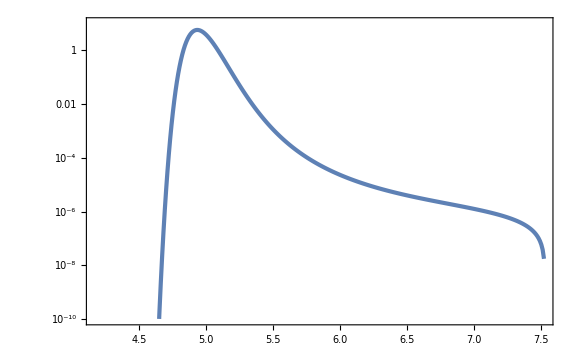

```mathematica
ListLogPlot[FPFTList,PlotRange->{10^-10,10}]
```

```mathematica
Nmin=4.5;
Nmax=7.5;
```

```mathematica
FPFTint[NN_]=Interpolation[FPFTList,InterpolationOrder->1][NN];
```

```mathematica
NIntegrate[FPFTint[NN],{NN,Nmin,Nmax}]
Nmean=NIntegrate[NN FPFTint[NN],{NN,Nmin,Nmax}]
varZ=NIntegrate[(NN-Nmean)^2 FPFTint[NN],{NN,Nmin,Nmax}]
Z3=NIntegrate[(NN-Nmean)^3 FPFTint[NN],{NN,Nmin,Nmax}]
Z4=NIntegrate[(NN-Nmean)^4 FPFTint[NN],{NN,Nmin,Nmax}]-3 varZ^2
```

1.00391

4.97525

0.00620648

0.000071113

0.0000732211

```mathematica
Nf//N
```

4.94956

```mathematica
fNL=5/18 Z3/varZ^2
```

0.512808

```mathematica
5/2//N
```

2.5

```mathematica
H3[x_]=x^3-3x;
H4[x_]=x^4-6 x^2+3;
```

```mathematica
FPFTGauss[NN_]=1/Sqrt[2π varZ] Exp[(-(NN-Nmean)^2)/(2varZ)];
FPFTEdge[NN_]=1/Sqrt[2π varZ](1+1/(3 2)Z3/varZ^(3/2)H3[(NN-Nmean)/Sqrt[varZ]]+1/(4 3 2)Z4/varZ^2 H4[(NN-Nmean)/Sqrt[varZ]])Exp[(-(NN-Nmean)^2)/(2varZ)];
```

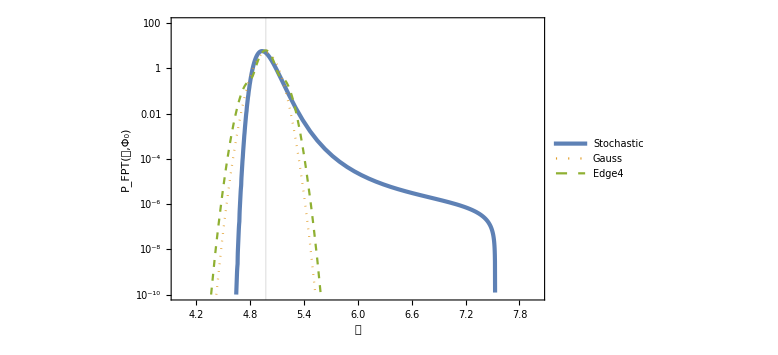

```mathematica
LogPlot[{FPFTint[NN],FPFTGauss[NN],FPFTEdge[NN]},{NN,4,8},PlotStyle->{AbsoluteThickness[3],Dotted,Dashed},PlotRange->{10^-10,10^2},FrameLabel->{𝒩,Subscript[P, FPT][𝒩,Subscript[Φ, 0]]},GridLines->{{Nmean},None},PlotLegends->Placed[LineLegend[{"Stochastic","Gauss","Edge4"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.75,0.75}]]
```

```mathematica
Ndrop=NN/.FindRoot[FPFTint[NN]==10^-9,{NN,7.4}]
```

7.5279

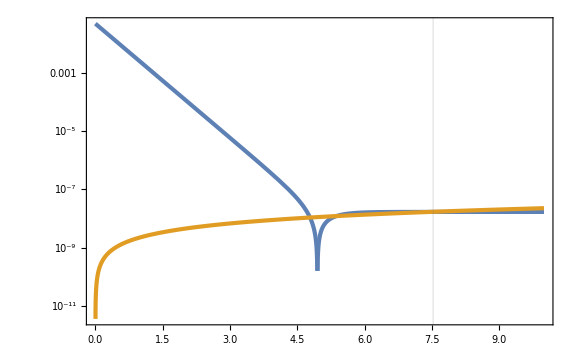

```mathematica
LogPlot[{Abs[B[NN]],Sqrt[2] H/(2π)NN},{NN,0,10},GridLines->{{Ndrop},None}]
```

```mathematica
NIntegrate[FPFTGauss[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTGauss[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTGauss[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTGauss[NN],{NN,Nmin,Nmax}]/Z3
```

1.

1.

1.

1.31905×10^-6

```mathematica
NIntegrate[FPFTEdge[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTEdge[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTEdge[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTEdge[NN],{NN,Nmin,Nmax}]/Z3
(NIntegrate[(NN-Nmean)^4 FPFTEdge[NN],{NN,Nmin,Nmax}]-3 varZ^2)/Z4
```

1.

1.

0.999997

1.00013

0.99994